```mathematica
(*Priklad 10 *)
```

```mathematica
-Graphics-
(*
Hodnoty součástek:C1=C2=100 nF,R1=0.1 Ω,L1=50 μH.
1. Spočítejte a vyneste do grafu vstupní impedanci obvodu pro 10^4≤ω≤10^8.
*)
```

-(10000000 ⅈ)/ω-(10000000 ⅈ (0.1+(ⅈ ω)/2000))/((0.1-(10000000 ⅈ)/ω+(ⅈ ω)/2000) ω)

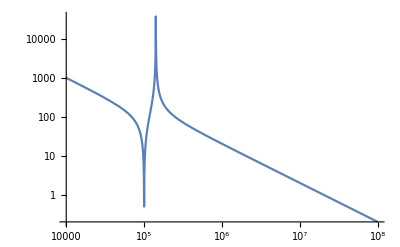

```mathematica
ClearAll["Global`*"]
C1=100*10^-9;
C2=100*10^-9;
R1 = 0.1;
L1 = 500*10^-6;

ZC1 = 1/(ⅉ*ω*C1);
ZC2 = 1/(ⅉ*ω*C2);
ZR1 = R1;
ZL1 = ⅉ*ω*L1;

ZR1L1 = ZR1+ZL1;
ZR1L1C2 = (ZR1L1*ZC2)/(ZR1L1+ZC2);
Zin = ZC1+ZR1L1C2
LogLogPlot[Abs[Zin],{ω,10^4,10^8}, PlotRange->All]
```

```mathematica
(*Příklad 11 *)
```

```mathematica
(*
Hodnoty součástek:R1=R3=0.1 Ω,R2=1000 Ω,L1=L2=1 mH,C1=1 μF.
1. Vykreslete přenos obvodu pro 1≤ω≤10^8.
*)
```

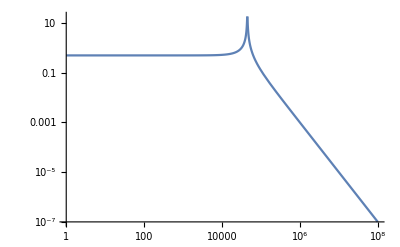

```mathematica
ClearAll["Global`*"]
R1=R3=0.1;
R2 = 1000;
L1=L2=1*10^-3;
C1 = 1*10^-6;

ZR1 = R1;
ZR2 = R2;
ZR3 = R3;
ZL1 = ⅉ*ω*L1;
ZL2 = ⅉ*ω*L2;
ZC1 = 1/(ⅉ*ω*C1);

ZR3L2 = ZR3+ZL2;
Zout = 1/(1/ZR2+1/ZR3L2+1/ZC1);

Zin = ZR1+ZL1+Zout;


Prenos = Zout/Zin;

LogLogPlot[Abs[Prenos],{ω,1,10^8}]
```

```mathematica
(* Příkad 13. cvičení *)
```

```mathematica
(*
Hodnoty součástek:R1=R2=0.1 Ω,C1=C2=100 μF,L1=50 μH,L2=500 nH.
1. Vykreslete přenos obvodu pro 1≤ω≤10^-8.
 2. Spočítejte a vyneste do grafu vstupní impedanci obvodu pro 1≤ω≤10^-8.
*)
```

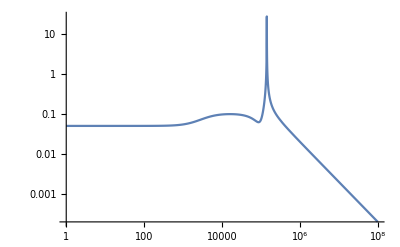

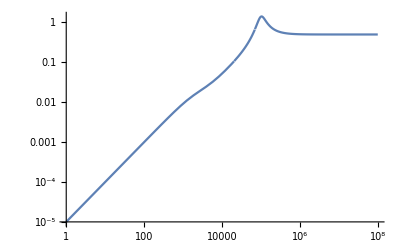

```mathematica
ClearAll["Global`*"]
R1=R2=0.1;
C1=C2=100*10^-6;
L1 = 50*10^-6;
L2 = 500*10^-9;

ZR1 = R1;
ZR2 = R2;
ZC1 = 1/(ⅉ*ω*C1);
ZC2 = 1/(ⅉ*ω*C2);
ZL1 = ⅉ*ω*L1;
ZL2 = ⅉ*ω*L2;

Zout = 1/(1/ZL2+1/ZC2);
ZR1L1 = ZR1+ZL1;

ZR2ZR1L1ZC1= 1/(1/ZR2+1/ZR1L1+1/ZC1);
Zin = ZR2ZR1L1ZC1+Zout;
Prenos = Zout/Zin;

LogLogPlot[Abs[Zin],{ω,1,10^8}]
LogLogPlot[Abs[Prenos],{ω,1,10^8}]
```

```mathematica
(* Příklad 14 *)
(* 
Impedance mezi dvěma svorkami je Z=2000+300j Ω. 
1. Určete parametry sériového náhradního schématu pro ω=100 s^-1 
2. Jaké to budou součástky a jaké budou mít parametry?
*)
ClearAll["Global`*"]
(* pomocné odvození *)

(*
    Zx = 12 +ⅉ*13
Zx1 = 120 -ⅉ*14

Rx = Re[Zx]
ZCx = 1/(ⅉ*ω*Cx)-> ⅉ/ⅉ*1/(ⅉ*ω*Cx)-> ⅉ/(ⅉ^2*ω*Cx)-> ⅉ/(-1*ω*Cx)-> -ⅉ*1/(ω*Cx)
ZLx = +ⅉ*ω*Lx
*)
ClearAll["Global`*"]
Z=2000+300*ⅉ;
R1 = Re[Z];
L1 = Im[Z]/ω/. ω->100;

Print["Obvod s impedancí Z =", Z, " [Ω], má náhradní zapojení, skládající se z rezistoru R1 = ", R1 , " Ω a z cívky s velikosí L1 = ", L1, " H."]
```

Obvod s impedancí Z =2000+300 ⅈ [Ω], má náhradní zapojení, skládající se z rezistoru R1 = 2000 Ω a z cívky s velikosí L1 = 3 H.

```mathematica
(* Příklad 15 *)
(* 
Impedance mezi dvěma svorkami je Z=800-500j Ω.
1. Určete parametry sériového náhradního schématu pro ω=10000 s^-1,2. jaké to budou součástky a jaké budou mít parametry?
*)
ClearAll["Global`*"]
Z=800-500*ⅉ;
R1 = Re[Z]
C1 = -1/(ω*Im[Z])/. ω-> 10^4//N
```

```mathematica
(* Příklad 16 *)
ClearAll["Global`*"]
(* 
Útlum první části kabelu je 7 dB,druhé 5 dB.
1. Jaký je celkový útlum v dB?
2. Jaké zesílení musí mít zesilovač (ve vyjádření bez decibelů-tedy kolikrát musí zesilovat),který má celkový útlum kompenzovat?
*)
utlum1 = 7; (* dB*)
utlum2 = 5;(* dB*)
utlumCelk = utlum1+utlum2; (* dB*)
zesileni = utlumCelk; (* dB*)
reseni = NSolve[zesileni==20*Log10[Prenos]]
```

{{Prenos→3.98107}}

```mathematica
(* Jak jeto s tema decibelama *)
zesileni/utlum ==20*Log[10,Uout/Uin]
ClearAll["Global`*"]
20*Log10[Prenos] == 20*Log[10,Prenos]
```

12/utlum==(20 Log[Uout/Uin])/Log[10]

True

```mathematica
číslo1 = 1000 ==10*10*10
číslo2 = 1000 == 10^3
číslo3 = Log10[1000]
```

True

True

3

```mathematica
(* Příklad 18 *)
-Graphics-

(*
Určete potřebné zesílení (zisk) zesilovače, který je potřeba, aby sériové zapojení: kabel-zeislovač-kabel udržel výstupní napětí U2 na hodnotě 5V.
Vstupní napětí U1 je 10V. 
Útlum prvního kabelu je 5 dB.
Útlum druhého kabelu je 3 dB.
Určete napětí na vstupních a výstupních svorkách zesilovače.
*)
```

```mathematica
ClearAll["Global`*"]
U1 = 10;
p1 = -5;
p2=-3;
U2=5;

rov1 = p1==20*Log10[Ua/U1];
Uax = Ua/.Solve[rov1,Ua][[1]]//N;
Print["Napětí na vstupu zesilovače je ", Uax, " V."]

rov2=p2==20*Log10[U2/Ub];
Ubx = Ub /. Solve[rov2,Ub][[1]]//N;
Print["Napětí na výstupu zesilovače je ", Ubx, " V."]

Vysledek = 20*Log10[Ubx/Uax];
Print["Zesílení (Zisk) = ", Vysledek, " dB."]
zesileni = Ubx/Uax; (* Prenos *)
Print["Přenos (poměr napětí) P = ", zesileni, "[-]."]
```

Napětí na vstupu zesilovače je 5.62341 V.

Napětí na výstupu zesilovače je 7.06269 V.

Zesílení (Zisk) = 1.9794 dB.

Přenos (poměr napětí) P = 1.25594[-].